```mathematica
Series[Exp[I s (y + f[y] h) ],{s,0,3}]
```

1+ⅈ (y+h f[y]) s-1/2 (y+h f[y])^2 s^2-1/6 ⅈ (y+h f[y])^3 s^3+O[s]^4

```mathematica
Series[ArcTan[y],{y,0,3}]
```

y-y^3/3+O[y]^4

```mathematica
Series[Sqrt[1 + y^2],{y,0,3}]
```

1+y^2/2+O[y]^4

```mathematica
Integrate[(ⅈ ⅇ^(-Abs[u]) √(π/2))/u Sin[u],{u,-1,1}]
```

1/2 √(π/2) (-3 ⅈ π-2 ExpIntegralEi[-1-ⅈ]+2 ExpIntegralEi[-1+ⅈ])

```mathematica
FourierTransform[Sqrt[1 + y^2],y,u]
```

-(√(2/π) BesselK[1,Abs[u]])/Abs[u]

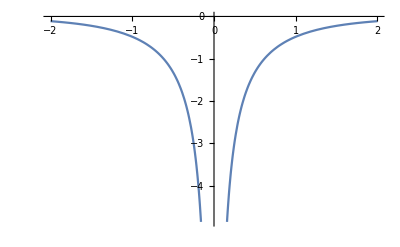

```mathematica
Plot[-√(2/π) BesselK[1,Abs[u]],{u,-2,2}]
```

```mathematica
N[%]
```

-1.98815